```mathematica
Quit[]
```

```mathematica
Needs["FeynArts`"]
Needs["FormCalc`"]
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
SetOptions[InsertFields, Model -> ToFileName[NotebookDirectory[],"modelFiles/SMS-stop_FA/SMS-stop_FA"],
GenericModel->ToFileName[NotebookDirectory[],"modelFiles/LorentzTadpole"],ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
processSMEFT = { V[4],V[4]} -> {-F[9], F[9]};
nameSMEFT = "SM-EFT";
topsSMEFT = CreateTopologies[1, 2-> 2];
insSMEFT = InsertFields[topsSMEFT, processSMEFT,LastSelections->{S[4]}];
```

generic model {/home/lessa/SMStoEFT/modelFiles/LorentzTadpole} initialized

classes model {/home/lessa/SMStoEFT/modelFiles/SMS-stop_FA/SMS-stop_FA} initialized

in total: 13 Particles insertions

```mathematica
processDMEFT = { V[4],V[4]} -> {F[13],F[13]};
nameDMEFT = "DM-EFT";
topsDMEFT = CreateTopologies[1, 2->2 ];
insDMEFT = InsertFields[topsDMEFT, processDMEFT];
```

in total: 18 Particles insertions

```mathematica
processSMS = { V[4],V[4]} -> {F[13], F[13],-F[9],F[9]};
nameSMS = "SMS";
topsSMS = CreateTopologies[0, 2-> 4];
insSMS = InsertFields[topsSMS, processSMS];
```

in total: 32 Particles insertions

```mathematica
FR$ClassesTranslation
```

{A→V[1],Z→V[2],W→V[3],G→V[4],ghA→U[1],ghZ→U[2],ghWp→U[3],ghWm→U[4],ghG→U[5],ve→F[1],vm→F[2],vt→F[3],e→F[4],mu→F[5],ta→F[6],u→F[7],c→F[8],t→F[9],d→F[10],s→F[11],b→F[12],H→S[1],G0→S[2],GP→S[3],chi→F[13],ST→S[4]}

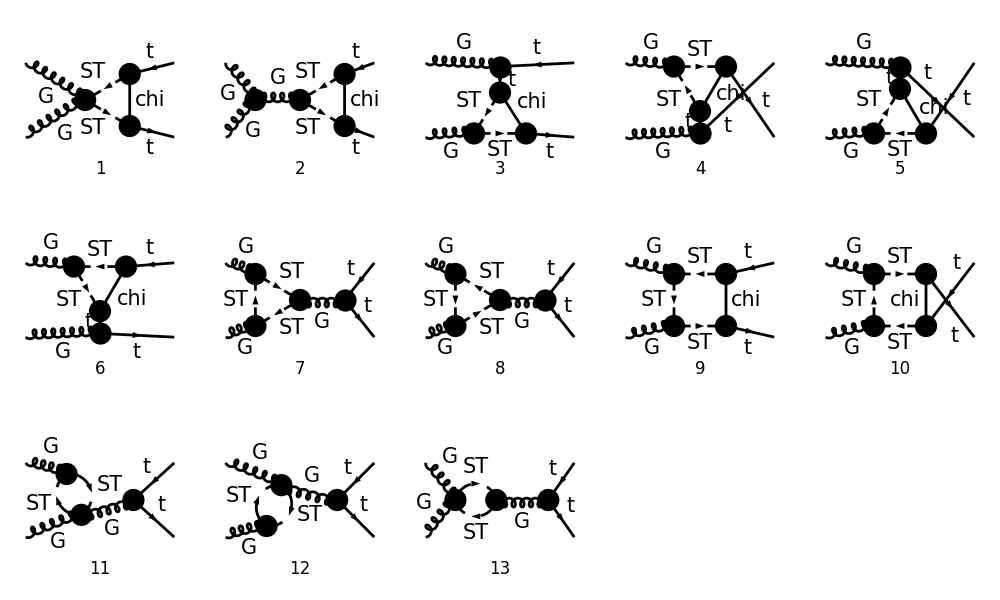

```mathematica
Paint[insSMEFT,ColumnsXRows->{5,3},ImageSize->{ 1000,600},PaintLevel->{Particles},SheetHeader->nameSMEFT,Numbering->Simple,AutoEdit->True];
```

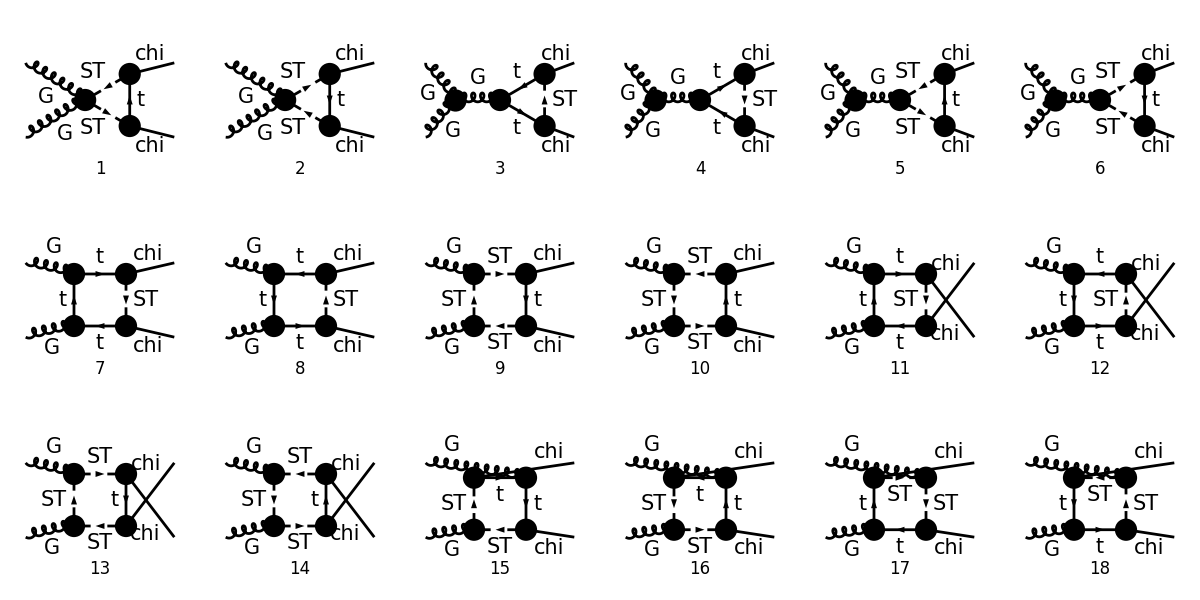

FeynArtsGraphics[DM-EFT][([1] | [2] | [3] | [4] | [5] | [6]
[7] | [8] | [9] | [10] | [11] | [12]
[13] | [14] | [15] | [16] | [17] | [18])]

```mathematica
Paint[insDMEFT,ColumnsXRows->{6,3},ImageSize->{ 1200,600},PaintLevel->{Particles},SheetHeader->nameDMEFT,Numbering->Simple,AutoEdit->True]
```

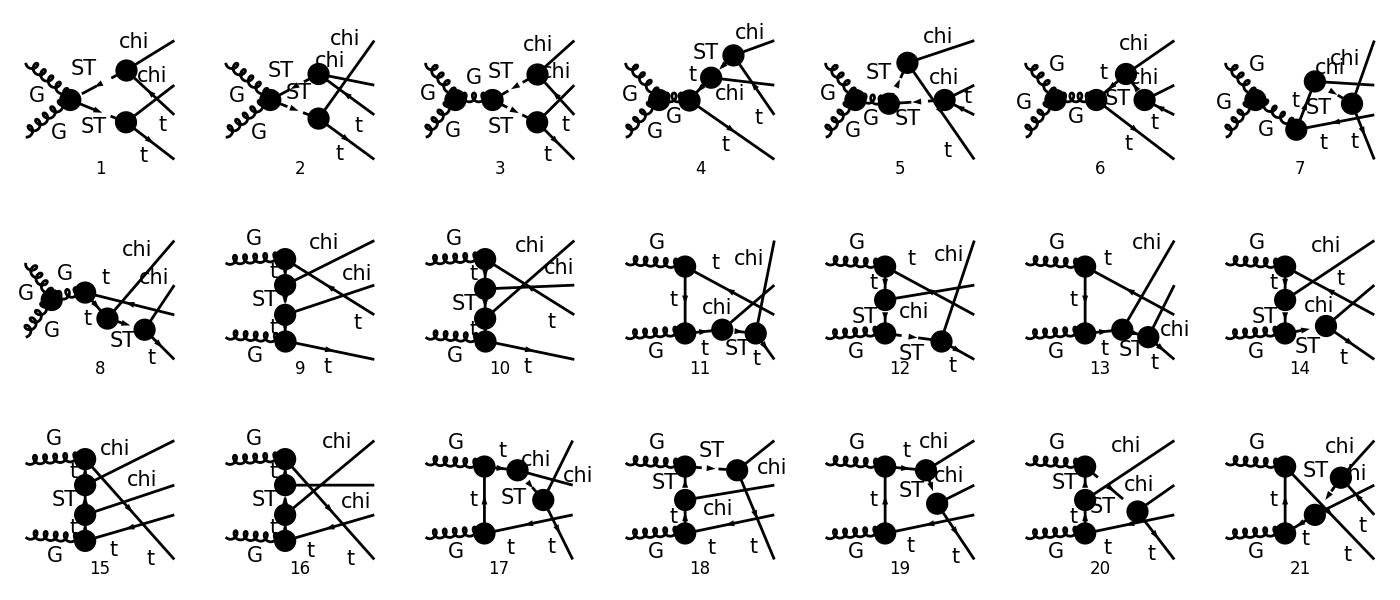

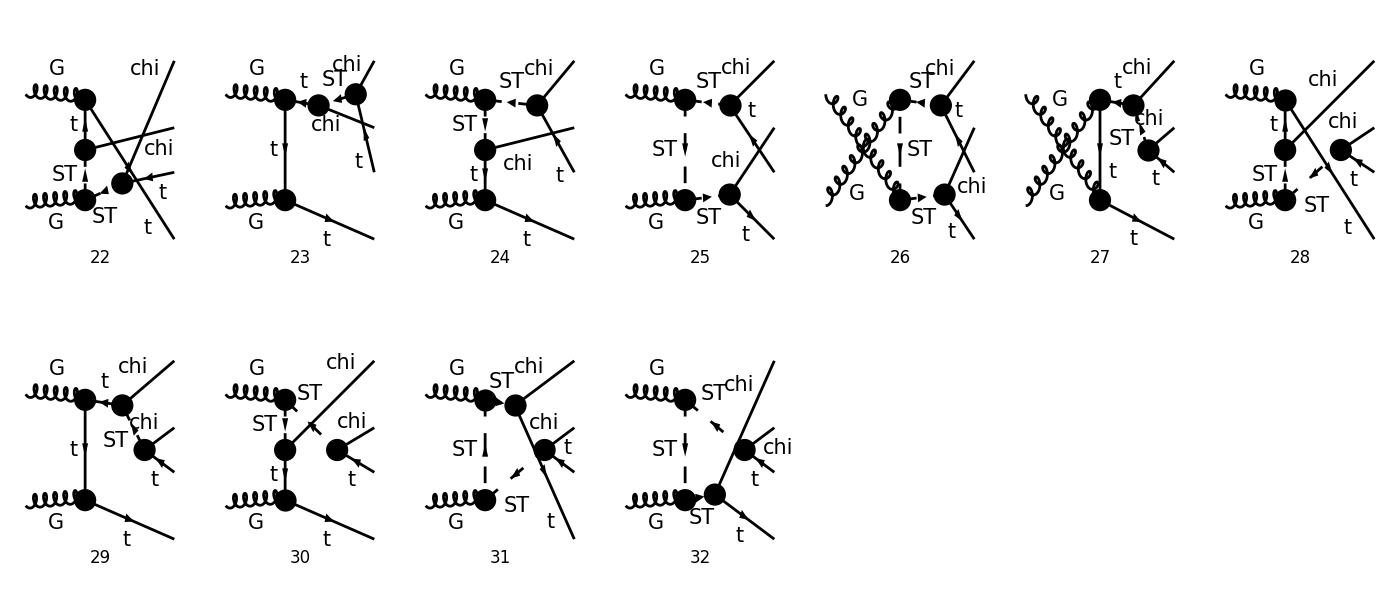

FeynArtsGraphics[SMS][([1] | [2] | [3] | [4] | [5] | [6] | [7]
[8] | [9] | [10] | [11] | [12] | [13] | [14]
[15] | [16] | [17] | [18] | [19] | [20] | [21]),([22] | [23] | [24] | [25] | [26] | [27] | [28]
[29] | [30] | [31] | [32] | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null)]

```mathematica
Paint[insSMS,ColumnsXRows->{7,3},ImageSize->{ 1400,600},PaintLevel->{Particles},SheetHeader->nameSMS,Numbering->Simple,AutoEdit->True]
```